# Arnold’s Cat Map.

## The discrete map acting on a two-dimensional lattice {x, y} where x and y are restricted to the integer values 0, 1, ..., c-1. Its solution introduces Fibonacci integers.

```mathematica
m={{1,1},{1,2}};m//MatrixForm
```

(1 | 1
1 | 2)

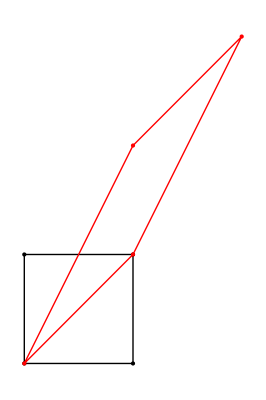

```mathematica
Graphics[{PointSize[Large],Point[{0,0}],Point[{0,1}],Point[{1,0}],Point[{1,1}],Line[{{0,0},{0,1},{1,1},{1,0},{0,0}}],Red,Point[m.{0,0}],Point[m.{0,1}],Point[m.{1,0}],Point[m.{1,1}],Line[{m.{0,0},m.{0,1},m.{1,1},m.{1,0},m.{0,0}}]}]
```

```mathematica
Clear[x,y];RSolve[{x[n]==x[n-1]+y[n-1],y[n]==x[n-1]+2y[n-1],x[0]==x0,y[0]==y0},{x[n],y[n]},n]//FullSimplify
```

{{x[n]→1/(√5)2^(-1-n) ((3-√5)^n (x0+√5 x0-2 y0)+(3+√5)^n ((-1+√5) x0+2 y0)),y[n]→1/(√5)2^(-1-n) (-(3-√5)^n (2 x0+y0-√5 y0)+(3+√5)^n (2 x0+y0+√5 y0))}}

```mathematica
MatrixPower[m,n].{x0,y0}//FullSimplify
```

{1/(√5)2^(-1-n) ((3-√5)^n (x0+√5 x0-2 y0)+(3+√5)^n ((-1+√5) x0+2 y0)),1/5 2^(-1-n) (-(3-√5)^n (2 √5 x0+(-5+√5) y0)+(3+√5)^n (2 √5 x0+(5+√5) y0))}

```mathematica
{{Fibonacci[2n-1],Fibonacci[2n]},{Fibonacci[2n],Fibonacci[2n+1]}}.{x0,y0}//FullSimplify
```

{y0 Fibonacci[2 n]+x0 Fibonacci[-1+2 n],x0 Fibonacci[2 n]+y0 Fibonacci[1+2 n]}

It should be clear that these three expressions are equivalent the latter because of the following identity :

```mathematica
((MatrixPower[m,n]//Flatten)==({{Fibonacci[2 n-1],Fibonacci[2 n]},{Fibonacci[2 n],Fibonacci[2 n+1]}}//Flatten)//Thread)//FunctionExpand//FullSimplify[#,Element[n,Integers]]&
```

{True,True,True,True}

```mathematica
Table[{k,Fibonacci[k]},{k,-1,20}]
```

{{-1,1},{0,0},{1,1},{2,1},{3,2},{4,3},{5,5},{6,8},{7,13},{8,21},{9,34},{10,55},{11,89},{12,144},{13,233},{14,377},{15,610},{16,987},{17,1597},{18,2584},{19,4181},{20,6765}}

## Periodic solutions of the continuous map (period N) :

```mathematica
Solve[{(Fibonacci[2N-1]-1)x0+Fibonacci[2N]y0==K c,Fibonacci[2N]x0+(Fibonacci[2N+1]-1)y0==L c},{x0,y0}]//FullSimplify
```

{{x0→(c (K+L Fibonacci[2 N]-K Fibonacci[1+2 N]))/(Fibonacci[2 N]^2-(-1+Fibonacci[-1+2 N]) (-1+Fibonacci[1+2 N])),y0→(c (L+K Fibonacci[2 N]-L Fibonacci[-1+2 N]))/(Fibonacci[2 N]^2-(-1+Fibonacci[-1+2 N]) (-1+Fibonacci[1+2 N]))}}

```mathematica
{x0->c(K+L Fibonacci[2 N]-K Fibonacci[1+2 N])/(Fibonacci[2 N+1]+Fibonacci[2N-1]-2),y0->c(L+K Fibonacci[2 N]-L Fibonacci[-1+2 N])/(Fibonacci[2 N+1]+Fibonacci[2N-1]-2)}     (*Simplified by hand*)
```

{x0→(c (K+L Fibonacci[2 N]-K Fibonacci[1+2 N]))/(-2+Fibonacci[-1+2 N]+Fibonacci[1+2 N]),y0→(c (L+K Fibonacci[2 N]-L Fibonacci[-1+2 N]))/(-2+Fibonacci[-1+2 N]+Fibonacci[1+2 N])}

```mathematica
Mod[{c(K+L Fibonacci[2 N]-K Fibonacci[1+2 N])/(Fibonacci[2 N+1]+Fibonacci[2N-1]-2),c(L+K Fibonacci[2 N]-L Fibonacci[-1+2 N])/(Fibonacci[2 N+1]+Fibonacci[2N-1]-2)}/.{N->10,K->1,L->1},c]/.c->8     (*Looks for a particular period-10 solution in the case, c=8*)
```

{1592/275,376/275}

```mathematica
Table[Mod[MatrixPower[m,n].{1592/275,376/275},8]//FullSimplify,{n,0,12}]         (*Checks the periodicity*)
```

{{1592/275,376/275},{1968/275,144/275},{192/25,56/275},{2168/275,24/275},{2192/275,16/275},{8/275,24/275},{32/275,56/275},{8/25,144/275},{232/275,376/275},{608/275,984/275},{1592/275,376/275},{1968/275,144/275},{192/25,56/275}}

## The discrete map acting on a two-dimensional lattice {x, y} where x and y are restricted to the integer values 0, 1, ..., c-1. Its solution introduces Fibonacci integers.

```mathematica
catMapR=Compile[{{pic, _Integer, 2}}, Table[pic[[Mod[x + y,Length[pic], 1],Mod[x + 2y, Length[pic], 1]]], {x, Length[pic]}, {y, Length[pic]}]];    (*Code by Henrique Zeleny in Wolfram Demonstration Project*)
```

```mathematica
Rpixels=ImageData[-Graphics-,"Bit"]/.{{1,1,1}->1,{0,0,0}->-1};
```

```mathematica
Length[Rpixels]
```

64

```mathematica
prune[mat_,n_]:=Transpose[Drop[Drop[Transpose[Drop[Drop[mat,n],-n]],n],-n]]              (*Amputates the exterior frame of the image discarding a band of width, n*)
```

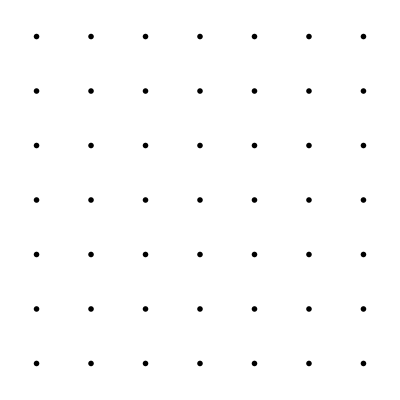

```mathematica
GraphicsGrid[Partition[Table[Image[Nest[catMapR,prune[Rpixels,0],k]],{k,0,49}],7]]
```

```mathematica
Manipulate[Image[Nest[catMapR,prune[Rpixels,0],iter]],{{iter,1,"iterations"},0,48,1,Appearance->"Labeled"},SaveDefinitions->True]
```

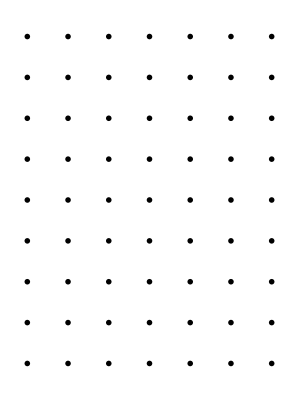
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[GraphicsGrid[Partition[Table[Image[Nest[catMapR,prune[Rpixels,j],k]],{k,0,63}],7]],{j,0,5}]
```

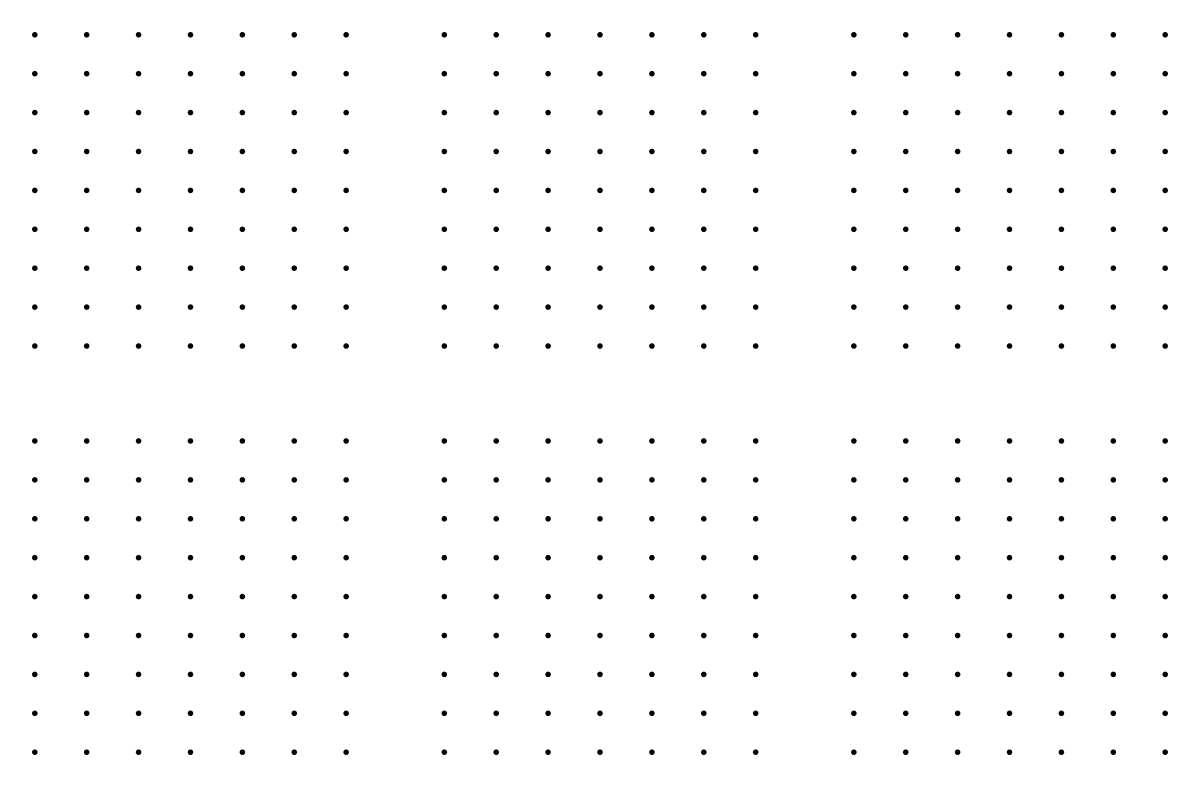

```mathematica
GraphicsGrid[Partition[Table[GraphicsGrid[Partition[Table[Image[Nest[catMapR,prune[Rpixels,j],k]],{k,0,63}],7]],{j,0,5}],3]]
```

## Prediction of the period as a function of c :

```mathematica
Table[n=1;While[Mod[Fibonacci[2n],c]≠0 || Mod[Fibonacci[2n-1],c]≠1 ,n++];{c,n},{c,64,54,-2}]
```

{{64,48},{62,15},{60,60},{58,21},{56,24},{54,36}}

```mathematica
Table[n=1;While[Mod[Fibonacci[2n],c]≠0 || Mod[Fibonacci[2n-1],c]≠1 ,n++];{c,n},{c,64,254,2}]
```

{{64,48},{66,60},{68,18},{70,120},{72,12},{74,114},{76,9},{78,84},{80,60},{82,60},{84,24},{86,132},{88,30},{90,60},{92,24},{94,48},{96,24},{98,168},{100,150},{102,36},{104,42},{106,54},{108,36},{110,30},{112,24},{114,36},{116,21},{118,87},{120,60},{122,30},{124,15},{126,24},{128,96},{130,210},{132,60},{134,204},{136,18},{138,24},{140,120},{142,105},{144,12},{146,222},{148,114},{150,300},{152,18},{154,120},{156,84},{158,39},{160,120},{162,108},{164,60},{166,84},{168,24},{170,90},{172,132},{174,84},{176,60},{178,66},{180,60},{182,168},{184,24},{186,60},{188,48},{190,90},{192,48},{194,294},{196,168},{198,60},{200,150},{202,75},{204,36},{206,312},{208,84},{210,120},{212,54},{214,36},{216,36},{218,54},{220,30},{222,228},{224,24},{226,114},{228,36},{230,120},{232,42},{234,84},{236,87},{238,72},{240,60},{242,165},{244,30},{246,60},{248,30},{250,750},{252,24},{254,384}}